# Projekt

## Pridobivanje podatkov

Podatke bom vzel iz Wolfram data repository.

```mathematica
podatki = ResourceData["Child Mortality from Malaria"];
```

## Analiza podatkov v Nigeriji, Kongu, Tanzaniji in Burkini Fasi

Te države sem si izbral, saj se tam zgodi skoraj 50% vseh smrtnih primerov zaradi malarije na svetovni ravni.

nigerijaPodatki = Select[podatki, #["Country"]== LinguisticAssistant&][[1]];
kongoPodatki = Select[podatki, #["Country"]== LinguisticAssistant&][[1]];
tanzanijaPodatki = Select[podatki, #["Country"]== LinguisticAssistant&][[1]];
burkinaFasoPodatki = Select[podatki, #["Country"]== LinguisticAssistant&][[1]];

```mathematica
drzave = {LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant};
drzaveVrstice=Select[podatki,MemberQ[ drzave,#["Country"]]&];
```

Prikaz števila smrtnih primerov za otroke v starostnem razponu 0 - 27 dni ter 0 - 4 let.

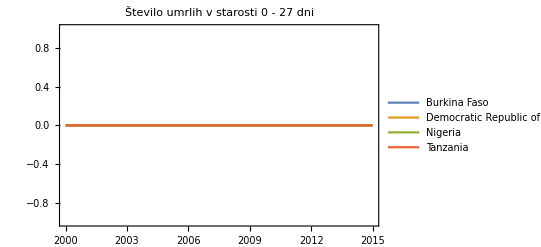

```mathematica
DateListPlot[#["Aged0To27Days"]&/@drzaveVrstice,PlotLegends->Table[drzaveVrstice[[x]]["Country"],{x,1,4}],PlotLabel->"Število umrlih v starosti 0 - 27 dni"]
```

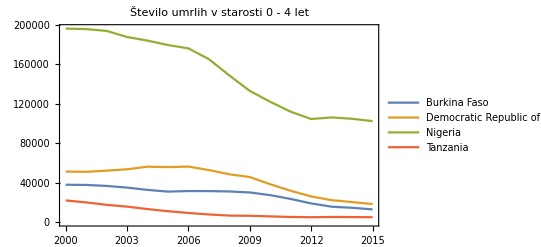

```mathematica
DateListPlot[#["Aged0To4Years"]&/@drzaveVrstice,PlotLegends->Table[drzaveVrstice[[x]]["Country"],{x,1,4}],PlotLabel->"Število umrlih v starosti 0 - 4 let"]
```